```mathematica
ClearAll["Global`*"]
```

```mathematica
ϵ0=1.33^2;(*діелектрична проникність рідини, в якій зважені наночастинки (вода)*)
ϵ1=1.59^2;(*д. п. наночастинки*)
ϵ2[δϵ_]=ϵ1+  δϵ;(*д. п. подвiйного електричноого шару*)*)
λ0=0.5145*10^(-6);
(*λ0=0.5785*10^(-6);*)
rad1=0.087/2*10^(-6);(*радiус наночастинки без урахування п. е. ш.*) 
rad2[δ_]=rad1(1+δ);(*її радiус з урахуванням п. е. ш.*)
(*η={{0.026,0.037,0.053,0.054,0.076,0.11}}; - на всякий случай*)
n[η_]:=η/(4 Pi rad1^3)*3;(*числова щiльнiсть диспергованих наночастинок; η - объ'ємна концентрацiя д. н.*)
d2[δ_]=2*rad2[δ];(*середнiй дiаметр наночастинки разом iз подвiйним шаром*)

k0=2 Pi / λ0;(* волновой вектор свiтла в вакуумi*) 
k=k0 √ϵ0;(*в. в. с. у водi*)
q[θ_]:=2 k Sin[θ/2](*измiна в. в. с. внаслiдок розсiювання в середi*)

aa1[θ_,ϵ1_]:=3((ϵ1-ϵ0)rad1)/((ϵ1+2ϵ0 )q[θ]^2)(Sin[q[θ] rad1]/(q[θ] rad1) - Cos[q[θ] rad1])(*ефективна поляризованiсть частинки без урахування п. е. ш.*)

aa2[θ_,ϵ1_,δϵ_,δ_]:=3((ϵ1-ϵ0)rad1)/((ϵ1+2ϵ0 )q[θ]^2)(Sin[q[θ] rad1]/(q[θ] rad1) - Cos[q[θ] rad1])+3(ϵ2[δϵ]-ϵ0)/((ϵ2[δϵ]+2ϵ0 )q[θ]^2)(rad2[δ](Sin[q[θ] rad2[δ]]/(q[θ]rad2[δ])-Cos[q[θ] rad2[δ]])-rad1(Sin[q[θ] rad1]/(q[θ] rad1)-Cos[q[θ] rad1]))(*е. п. ч. з урахуванням п. е. ш.*)

α[η_]:=(2η +1)^2/(1-η)^4;
β[η_]:=-(6 η(η/2+1)^2)/(1-η)^4;
γ[η_]:=(α [η]*η)/2;
c[θ_,η_,δ_]:=(4π d2[δ])/q[θ]^2((α [η]+β[η]+γ[η])(Cos[q[θ] d2[δ]]-Sin[q[θ] d2[δ]]/(q[θ] d2[δ]))-β[η](Sin[q[θ] d2[δ]]/(q[θ] d2[δ])+2 (Cos[q[θ] d2[δ]]-1)/(q[θ]^2 d2[δ]^2))-γ[η](3 Sin[q[θ] d2[δ]]/(q[θ] d2[δ])+12 Cos[q[θ] d2[δ]]/(q[θ]^2 d2[δ]^2)-24 Sin[q[θ] d2[δ]]/(q[θ]^3 d2[δ]^3)-24 (Cos[q[θ] d2[δ]]-1)/(q[θ]^4 d2[δ]^4))) ;(*Фур'є-образ прямої кореляцiйної функцiї*)
struc[θ_,η_,δ_]:=1/(1-n [η]*c[θ,η,δ]);(*структурний фактор твердих куль в наближеннi Перкуса-Йевiка*)
l1[ϵ1_,η_,δ_]:=1/(2 Pi k0^4 ϵ0^2/2  * NIntegrate[Sin[θ] (1+Cos[θ]^2)Abs[aa1[θ,ϵ1]]^2 n [η]*struc[θ,η,δ],{θ,0.001,Pi}]);(*довжина вiльного пробiгу фотона без урахування п. е. ш.*)
l2[ϵ1_,δϵ_,η_,δ_]:=1/(2 Pi k0^4 ϵ0^2/2  * NIntegrate[Sin[θ] (1+Cos[θ]^2)Abs[aa2[θ,ϵ1,δϵ,δ]]^2 n[η] *struc[θ,η,δ],{θ,0.001,Pi}]);(*д.в.п.ф. з урахуванням п. е. ш.*)
M[ϵ1_,δϵ_,η_,δ_]:=l2[ϵ1,δϵ,η,δ]/l1[ϵ1,η,δ];


(*далi представлено графiки залежностi M вiд δ(товщини шару)*)
```

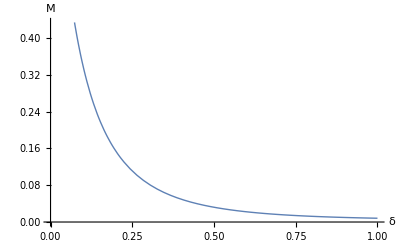

```mathematica
Plot[M[ϵ1,1.5,0.068,δ],{δ,0, 1},PlotStyle->Directive[Thick],
AxesLabel->{δ, M},BaseStyle->FontSize->16]
```

```mathematica
(*з отриманих залежностей можна бачити, що з ростом δ, величина довжини вiльного пробiгу фотона швидко спадає*)
```